( | 1 | 2 | 3 | 4 | 5 | 6
1 | 1 | 1 | 0 | 0 | 0 | 0
2 | 0 | 1 | 1 | 0 | 0 | 0
3 | 0 | 0 | 1 | 1 | 0 | 1
4 | 0 | 0 | 0 | 1 | 1 | 0
5 | 0 | 0 | 0 | 0 | 1 | 0
6 | 1 | 0 | 0 | 0 | 0 | 1)

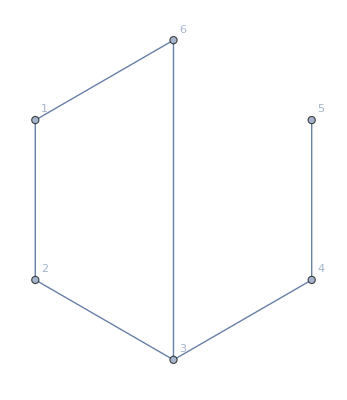

APL: 29/15

```mathematica
ClearAll["Global`*"]
(*----------2 Rewireing Networks----------*)
(*----------Basic Setup----------*)
n=6; (*SETUP the number of nodes*)
r=10; (*SETUP the percentage of rewireings[%]*)
rEnable=True; (*ENABLES the randomisation (disables the manuell mode)*)
debugEnable=False; (*ENABLES the debug mode (more output)*)

(*----------Setup a basic matrix with n nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*Change the structure of the default matrix*)
(*2nd edge*)
m[[n,2]]=0;
m[[2,2]]=1;
(*1st edge*)
m[[2,1]]=0;
m[[n,1]]=1;


(*-----Manipulation of the matrix------*)
If[rEnable,
Do[
(*pick a random edge to change*)
pickEdge=Random[Integer,{1,n}];
If[debugEnable,Print["Edge:",pickEdge]];

(*find a changable node*)
changeNode=0;
For[i=1,i<n+1,i++,
If[m[[i,pickEdge]]==1 && i≠pickEdge ,
changeNode=i;
];
];
If[debugEnable,Print["Change Node:",changeNode]];

(*find a new random node for the edge to connect*)
(Label[newRandom];
newNode=Random[Integer,{1,n}];
If[debugEnable,Print["New Node:",newNode]];
(*check if the changenode is the new node (loop)*)
If[newNode == changeNode || newNode==pickEdge,
If[debugEnable,Print["Same Node"]];
Goto[newRandom];
,Goto[nodeCheck];
];
Label[nodeCheck];
(*check if the new node create only a NEW connection*)
For[i=0,i<n+1,i++,
If[m[[pickEdge,newNode]]==1,
If[debugEnable,Print["Same Connection"]];
Goto[newRandom];
,Goto[connectionCheck];
];
];
Label[connectionCheck];
(*change the connection*)
(*change the connection*)
rollbackChange=m[[changeNode,pickEdge]];
rollbackNew=m[[newNode,pickEdge]];
m[[changeNode,pickEdge]]=0;
m[[newNode,pickEdge]]=1;

(*if the new connection causes a dead end: rollback*)
If[MeanGraphDistance[IncidenceGraph[m]]≥Infinity, 
If[debugEnable,Print[Red,"Infinity_Alert"]];
m[[changeNode,pickEdge]]=rollbackChange;
m[[newNode,pickEdge]]=rollbackNew;
Goto[newRandom];
,Goto[confirmedPoint];
];
Label[confirmedPoint]);
,Round[n/100*r]];
(*-----Manuell Mode-----*)
(*m[[OldNode,Edge]]=0;
m[[newNode,Edge]]=1;*)
,m[[n,1]]=0;
m[[3,1]]=1;
(*...*)
];

(*-----Functions-----*)


(*-----Output------*)
matrixLabel=Table[x,{x,n}];
MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]
IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];
m=IncidenceGraph[m];
Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]
Print["APL: ",MeanGraphDistance[m]]
```